# SumOfIntegerPowers

Express an integer or infinite quantity as a sum of powers of one or more integers

## Definition

### Auxiliary Functions for Powers of a Single Integer

```mathematica
ClearAll[iSingleIntegerList,iSingleIntegerPowers,iSingleIntegerCoeffs]

iSingleIntegerList[n_?(IntegerQ[#]&&#>=0&)]:=iSingleIntegerList[n,2];

iSingleIntegerList[Infinity,q_Integer]:=Return[{{q,Infinity}}];

iSingleIntegerList[n_?(IntegerQ[#]&&#>=0&),q_Integer]:=Module[
{
	n1=n,powers={},p,pp=ResourceFunction["PerfectPower"]
},
	(* n==∞ is a base case *)
	If[n==Infinity,
		Return[{{q,Infinity}}];
		(* Return[{{q,Inactivate[-Infinity]}}]; *)
	];
	
	(* n==0 is a base case *)
	If[n==0,
		Return[{{q,-Infinity}}];
		(* Return[{{q,Inactivate[-Infinity]}}]; *)
	];
	
	(* n==1 is a base case *)
	If[n==1,
		Return[{{q,0}}];
	];
	
	(* n==q is a base case *)
	If[n==q,
		Return[{{q,1}}];
	];
	
	(* n==q^α is a base case *)
	If[MemberQ[pp[n][[All,1]],q],
		Return[{{q,Log[q,n]}}];
	];
	
	While[n1!=0,
		p=Floor[Log[q,n1]];
		powers=Append[powers,p];
		n1=n1-q^p;
	];
	
	Return[
		Transpose[{
			ConstantArray[q,Length[powers]],
			powers
		}]
	];
]

iSingleIntegerPowers[a___]:=Block[
{
	list=iSingleIntegerList[a],
	tal
},
	If[Dimensions[tal=(Tally[list])[[All,1]]]=={2},
		Return[{tal}],
		Return[tal]
	];
];

iSingleIntegerCoeffs[a___]:=Block[
{
	list=iSingleIntegerList[a]
},
	If[Dimensions[list]=={2},
		Return[{1}],
		Return[Tally[list][[All,2]]]
	];
];
```

### Auxiliary Functions for Powers of Multiple Integers

```mathematica
ClearAll[iMultiIntegerList,iMultiIntegerPowers,iMultiIntegerCoeffs]

Options[iMultiIntegerList]={
	"HoldListProducts"->False
};

(*iMultiIntegerList[n_?(IntegerQ[#]&&#>=0&)]:=iMultiIntegerList[n,2];*)

iMultiIntegerList[Infinity,list:{__?(IntegerQ[#]&&#>1&)},opts:OptionsPattern[]]:=Return[Join[Transpose[{list,ConstantArray[Infinity,Length[list]]}],{{0}}]];
iMultiIntegerList[-Infinity,list:{__?(IntegerQ[#]&&#>1&)},opts:OptionsPattern[]]:=Return[Join[Transpose[{list,ConstantArray[Infinity,Length[list]]}],{{0}}]];

iMultiIntegerList[n_?(IntegerQ[#]&&#>=0&),list:{__?(IntegerQ[#]&&#>1&)},opts:OptionsPattern[]]:=Module[{
	(* Functions *)
	maxat=ResourceFunction["PositionLargest"][#]&,
	ifi=ResourceFunction["InactiveFactorInteger"],
	PrimeMultipleOfCertainPrimesQ,
	(* Constants *)
	n1,holdprod=OptionValue["HoldListProducts"],done=False,
	(* Lists *)
	primes=list,
	floors={},primeprods={},coeffs={},exps={},powers={}
	
},
	PrimeMultipleOfCertainPrimesQ[k_?(IntegerQ[#]&&#>0&),p_List]:= SubsetQ[p,FactorInteger[k][[All,1]]];
	n1=n;
	
	(* n==0 is a base case *)
	If[n==0,
		(* Return[{Transpose[{list,ConstantArray[Inactivate[-Infinity],Length[list]]}]}];*)
		(* Return[{{First@primes,Inactivate[-Infinity]},{0}}]; *)
		Return[Join[Transpose[{list,ConstantArray[-Infinity,Length[list]]}],{{0}}]];
	];
	
	(* n==∞ is a base case *)
(*	If[n==Infinity,
		(* Return[{Transpose[{list,ConstantArray[Inactivate[-Infinity],Length[list]]}]}];*)
		(* Return[{{First@primes,Inactivate[-Infinity]},{0}}]; *)
		Return[Join[Transpose[{list,ConstantArray[Infinity,Length[list]]}],{{0}}]];
	];*)
	
	(* n==1 is a base case *)
	If[n==1,
		Return[{{First@primes,0},{0}}];
	];
	
	(* n∈primes is a base case *)
	If[MemberQ[primes,n],
		Return[{{n,1},{0}}];
	];
	
	(* n==((product of primes)) may be a base case *)	
	If[!MemberQ[n,primes] && holdprod==True && PrimeMultipleOfCertainPrimesQ[n1,primes],
	(
		done=True;
		Return[{{0,1},{ifi[n1]}}];
	)
	];
	
	While[n1!=0 && n1!=1 && (!PrimeMultipleOfCertainPrimesQ[n1,primes] || (PrimeMultipleOfCertainPrimesQ[n1,primes] && done==False)),(* && !PrimeMultipleOfCertainPrimesQ[n1,primes],*)
		floors=Floor[Log[#,n1]]&/@primes;
		primeprods=MapThread[Power,{primes,floors}];
		i=maxat[primeprods];
		coeffs=Append[coeffs,primes[[i]]];
		exps=Append[exps,floors[[i]]];
		n1=n1-primeprods[[i]];
	];
	
	powers=Transpose[{coeffs,exps}];
	
	If[n1==0,
		powers=Append[powers,{0}];
	];
	
	If[n1==1,
	(
		powers=Append[powers,{Min@list,0}];
		powers=Append[powers,{0}];
	)
	];
	
	If[PrimeMultipleOfCertainPrimesQ[n1,primes],
		powers=Append[powers,{ifi[n1],1}];
	];
	
	(* Note: powers[[-1]] is the constant term! *)
	Return[powers];
];

iMultiIntegerPowers[a___]:=Block[{list=iMultiIntegerList[a]}, Return[Tally[list][[All,1]]];];
iMultiIntegerCoeffs[a___]:=Block[{list=iMultiIntegerList[a]}, Return[Tally[list][[All,2]]];];
```

### Main Definitions

```mathematica
ClearAll[SumOfIntegerPowers]

Options[SumOfIntegerPowers]={
	"Collect"->False,
	"FactorNegative"->False,
	"HoldListProducts"->False
};

SumOfIntegerPowers[n_?(IntegerQ[#]||#==Infinity||#==-Infinity&),opts:OptionsPattern[]]:=SumOfIntegerPowers[n,2,opts];

SumOfIntegerPowers[list:{__?(IntegerQ[#]||#==Infinity||#==-Infinity&)},q_Integer,opts:OptionsPattern[]]:=SumOfIntegerPowers[#,q,opts]&/@list/;Length[list]>1;

SumOfIntegerPowers[n_?(IntegerQ[#]||#==Infinity||#==-Infinity&),q_Integer,opts:OptionsPattern[]]:=Module[{
	list,pow,coeff,op,neg=False,coll=OptionValue["FactorNegative"]
},
	(* Handle negative n first because aux functions don't accept negative inputs *)
	If[n<0 && coll==True,
		Return[Inactive[Times][-1,SumOfIntegerPowers[-n,q,opts]]];
	];
	
	If[n<0 && coll==False,
	(
		neg=True;
		list=iSingleIntegerList[-n,q];
		pow=iSingleIntegerPowers[-n,q];
		coeff=-1*iSingleIntegerCoeffs[-n,q];
	),
	(
		list=iSingleIntegerList[n,q];
		pow=iSingleIntegerPowers[n,q];
		coeff=iSingleIntegerCoeffs[n,q];
	)
	];
	
	If[OptionValue["Collect"]==True,
	(
		op=Inactive[Power]@@@pow;
			
		op=If[coeff[[#]]==1,
			op[[#]],
			If[neg==False && coll==False,
				Inactive[Times][coeff[[#]],op[[#]]],
				Times[coeff[[#]],op[[#]]]
			]
		]&/@Range[1,Length[op]];
			
		op=If[Length[op]==1,
			First@op,
			Inactive[Plus]@@op
		];
	),
	(
		op=Inactive[Power]@@@list; (* can include HoldForm here for better-looking exponents (see below) *)
		
		If[neg==True && coll==False,
			op=-1*op;
		];
			
		op=If[Length[op]==1,
			First@op,
			Inactive[Plus]@@op
		];
	)
	];
	
	Return[op];
];

SumOfIntegerPowers[n:{__?(IntegerQ[#]||#==Infinity||#==-Infinity&)},list:{__?(IntegerQ[#]&&#>1&)},opts:OptionsPattern[]]:=SumOfIntegerPowers[#,First@list,opts]&/@n/;Length[list]==1;

SumOfIntegerPowers[n:{__?(IntegerQ[#]||#==Infinity||#==-Infinity&)},list:{__?(IntegerQ[#]&&#>1&)},opts:OptionsPattern[]]:=SumOfIntegerPowers[#,list,opts]&/@n;

SumOfIntegerPowers[n_?(IntegerQ[#]||#==Infinity||#==-Infinity&),list:{__?(IntegerQ[#]&&#>1&)},opts:OptionsPattern[]]:=SumOfIntegerPowers[n,First@list,opts]/;Length[list]==1;

SumOfIntegerPowers[n_?(IntegerQ[#]||#==Infinity||#==-Infinity&),list:{__?(IntegerQ[#]&&#>1&)},opts:OptionsPattern[]]:=Module[{
	(* ifi=ResourceFunction["InactiveFactorInteger"],*)
	pairs,pow,coeff,
	op,const,oldpow,
	neg=False,coll=OptionValue["FactorNegative"]
},
	(* Handle negative n first because aux functions don't accept negative inputs *)
	If[n<0 && coll==True,
		Return[Inactive[Times][-1,SumOfIntegerPowers[-n,list,opts]]];
	];
	
	If[n<0 && coll==False,
	(
		neg=True;
		pairs=iMultiIntegerList[-n,list,"HoldListProducts"->OptionValue["HoldListProducts"]];
		pow=iMultiIntegerPowers[-n,list];
		coeff=-1*iMultiIntegerCoeffs[-n,list];
	),
	(
		pairs=iMultiIntegerList[n,list,"HoldListProducts"->OptionValue["HoldListProducts"]];
		pow=iMultiIntegerPowers[n,list];
		coeff=iMultiIntegerCoeffs[n,list];
	)
	];
	
	(* If n is a product of primes, return the product and do nothing else *)
	If[pairs[[1,1]]==0,
		Return[First@pairs[[2]]];
	];
	
	If[OptionValue["Collect"]==True,
	(	
		oldpow=pow;
		pow=DeleteCases[pow,_?(#=={0}&)];
		coeff=coeff[[;;-(Length[oldpow]-Length[pow]+1)]];
			
		op=If[Head[Head[#1]]=!=Inactive,
			Inactive[Power][#1,#2],
			#1
		]&@@@pow;
				
		op=If[coeff[[#]]==1,
			op[[#]],
			If[neg==False,
				Inactive[Times][coeff[[#]],op[[#]]],
				Times[coeff[[#]],op[[#]]]
			]
		]&/@Range[1,Length[op]];
			
		If[const!=0,
			op=Append[op,const];
		];
			
		If[Length[op]>1,
			op=Inactive[Plus]@@op,
			op=First@op
		];
	),
	(
(*		Print["Old pairs: "<>ToString[pairs]];*)
		
		const=First@pow[[-1]];
		pairs=pairs[[;;-2]];
		pow=pow[[;;-2]];
		coeff=coeff[[;;-2]];
		
		If[const=!=0,
			pairs=Append[pairs,{const,1}];
		];
		
(*		Print["New pairs: "<>ToString[pairs]];
		
		Print[const]; Print[pow]; Print[coeff];*)
		
		op=If[Head[Head[#1]]=!=Inactive,
			Inactive[Power][#1,#2], (* HoldForm[Power[#1,#2]],*)
			#1
		]&@@@pairs;
			
		If[neg==True && coll==False,
			op=-1*op;
		];
			
		If[Length[op]>1,
			op=Inactive[Plus]@@op,
			op=First@op
		];
	)
	];
	
	Return[op];
];
```

## Documentation

### Usage

SumOfIntegerPowers[n,{p_1,…,p_k}]

gives an Inactive factorization p_1^n_1+p_2^n_2+p_k^n_k of n=p_1^n_1+p_2^n_2+p_k^n_k.

SumOfIntegerPowers[n,m]

gives an Inactive factorization m^n_1+m^n_2+m^n_k of n=m^n_1+m^n_2+m^n_k.

SumOfIntegerPowers[n,{m}]

is equivalent to SumOfIntegerPowers[n,m].

SumOfIntegerPowers[{n_1,…,n_k},arg]

gives a List of Inactive factorizations equivalent to {SumOfIntegerPowers[n_1,arg],…,SumOfIntegerPowers[n_k,arg]}.

SumOfIntegerPowers[n]

is equivalent to SumOfIntegerPowers[n,2].

SumOfIntegerPowers[list]

is equivalent to SumOfIntegerPowers[#,2]&/@list.

### Details & Options

SumOfIntegerPowers allows an integer or List of integers to be decomposed as a sum of powers of one or more integers.

By default, SumOfIntegerPowers[n,{p_1,…,p_k}] generally performs the following algorithm to determine the factorization of n:

Determine the largest integers α_1,…,α_k for which p_1^α_1,…,p_k^α_k all divide n.

Compute m_1=Max[p_1^α_1,…,p_k^α_k]. m_1 is the first term of the factorization of n.

Repeat the the process for n_1=n-m_1 to find the second term of the factorization.

Continue iterating until the resulting integer n_β either equals 0 or 1.

For integers n, SumOfIntegerPowers[n,list] requires that list consist only of integers greater than 1.

For positive integers n, SumOfIntegerPowers[-n,list] effectively returns -1 times the factorization returned by SumOfIntegerPowers[n,list].

SumOfIntegerPowers[0,{p_1,…,p_k}] returns the inactivated sum p_1^(-∞)+⋯+p_k^(-∞).

SumOfIntegerPowers[Infinity,list] and SumOfIntegerPowers[-Infinity,list] both work whenever list consists only of integers greater than 1. SumOfIntegerPowers[Infinity,{p_1,…,p_k}] returns the inactivated sum p_1^∞+⋯+p_k^∞ and SumOfIntegerPowers[-Infinity,{p_1,…,p_k}] returns -1 times that.

SumOfIntegerPowers accepts the following options (which may tweak the above-mentioned algorithm):

"Collect" | False | whether like terms in the decomposition should be collected
"FactorNegative" | False | whether existing negative signs should be "factored out" of the resulting decomposition
"HoldListProducts" | False | whether the above-described algorithm should halt when a product of list elements is reached

## Examples

### Basic Examples

Start with a random integer:

```mathematica
int0=RandomInteger[{10^15,10^20}]
```

38665763589460525258

Express it as a sum of powers of 7, 11 and 13:

```mathematica
sum0=SumOfIntegerPowers[int0,{7,11,13}]
```

7^23+13^17+13^16+13^16+13^16+7^21+7^20+7^19+11^14+7^17+7^14+11^11+7^13+11^10+11^9+11^9+11^9+11^9+7^10+7^10+13^7+13^7+7^9+7^8+13^6+13^5+7^6+13^4+7^4+7^4+7^4+7^4+7^4+7^3+13^1+13^1+7^0+7^0

Confirm the result:

```mathematica
Activate[sum0]==int0
```

True

Define an integer:

```mathematica
int1=12345;
```

Express it as the sum of powers of 4:

```mathematica
sum1=SumOfIntegerPowers[int1,4]
```

4^6+4^6+4^6+4^2+4^2+4^2+4^1+4^1+4^0

Confirm the result:

```mathematica
Activate[sum1]==int1
```

True

The same result can be achieved using {4} as a second argument instead of 4:

```mathematica
Activate[sum1]==int1==Activate[SumOfIntegerPowers[int1,{4}]]
```

True

Define a new (large) integer:

```mathematica
int2=2*3*Factorial[1234];
```

Express it as the sum of (many) powers of 2 using a two-argument form and use Shallow to show a small snippet of the result:

```mathematica
sum2=SumOfIntegerPowers[int2,2];
Shallow[sum2]
```

2^10900+2^10899+2^10898+2^10896+2^10892+2^10890+2^10887+2^10886+2^10882+2^10881+«4716»

The same can be achieved using the one-argument form:

```mathematica
sum2b=SumOfIntegerPowers[int2];
Shallow[sum2b]
```

2^10900+2^10899+2^10898+2^10896+2^10892+2^10890+2^10887+2^10886+2^10882+2^10881+«4716»

Confirm the results:

```mathematica
Activate[sum2]==int2==Activate[sum2b]
```

True

### Scope

SumOfIntegerPowers works with negative numbers:

```mathematica
neg=-RandomInteger[{10^15,10^20}]
```

-614373854267014960

```mathematica
negsum=SumOfIntegerPowers[neg,{3,19}]
```

-3^37+-3^36+-3^33+-3^33+-19^12+-3^31+-3^28+-3^28+-19^9+-3^23+-3^22+-3^19+-3^18+-3^17+-3^17+-3^15+-3^14+-3^14+-3^13+-3^11+-3^10+-3^7+-3^6+-19^2+-3^5+-19^1

```mathematica
Activate[negsum]==neg
```

True

SumOfIntegerPowers[0,…] works with both non-List and List second arguments. In the prior case, SumOfIntegerPowers[0,q] returns an Inactive version of Power[q,-Infinity]:

```mathematica
zerosuma=SumOfIntegerPowers[0,791]
```

791^(-∞)

```mathematica
Activate[zerosuma]
```

0

In the latter case, SumOfIntegerPowers[0,{a_1,…,a_n}] returns an Inactive form of Power[a_1,-Infinity]+⋯+Power[a_n,-Infinity]:

```mathematica
zerosumb=SumOfIntegerPowers[0,Prime/@Range[5]]
```

2^(-∞)+3^(-∞)+5^(-∞)+7^(-∞)+11^(-∞)

```mathematica
Activate[zerosumb]
```

0

SumOfIntegerPowers[Infinity,…] and SumOfIntegerPowers[-Infinity,…] both work as expected. Here are some computations with Infinity:

```mathematica
SumOfIntegerPowers[Infinity,Prime/@Range[2,7]]
```

3^∞+5^∞+7^∞+11^∞+13^∞+17^∞

```mathematica
Activate[%]
```

∞

```mathematica
SumOfIntegerPowers[Infinity,12321]
```

12321^∞

```mathematica
Activate[%]
```

∞

```mathematica
SumOfIntegerPowers[Infinity]
```

2^∞

```mathematica
Activate[%]
```

∞

Here are some with -Infinity:

```mathematica
SumOfIntegerPowers[-Infinity,Fibonacci/@Range[3,7]]
```

-2^∞+-3^∞+-5^∞+-8^∞+-13^∞

```mathematica
Activate[%]
```

-∞

```mathematica
SumOfIntegerPowers[-Infinity,1111]
```

-1111^∞

```mathematica
Activate[%]
```

-∞

```mathematica
SumOfIntegerPowers[-Infinity]
```

-2^∞

```mathematica
Activate[%]
```

-∞

Both Infinity and -Infinity work as elements of first-argument lists as well:

```mathematica
Join[{{Style["input",Bold],"   ",Style["decomp",Bold],"   ",Style["equal?",Bold]}},{Activate[#],"   ",#,"   ",Activate[#==#]}&/@SumOfIntegerPowers[{75,-Infinity,-91,Infinity,0},Fibonacci/@Range[3,7]]]//Grid[#,Dividers->{False,All},FrameStyle->Dotted]&
```

input |     | decomp |     | equal?
75 |     | 2^6+3^2+2^1 |     | True
-∞ |     | -2^∞+-3^∞+-5^∞+-8^∞+-13^∞ |     | True
-91 |     | -3^4+-3^2+-2^0 |     | True
∞ |     | 2^∞+3^∞+5^∞+8^∞+13^∞ |     | True
0 |     | 2^(-∞)+3^(-∞)+5^(-∞)+8^(-∞)+13^(-∞) |     | True

SumOfIntegerPowers[list_1,list_2] threads over list_2 and equals SumOfIntegerPowers[#,list_2]&/@list_1:

```mathematica
list1={55,79,123}; list2={2,3,5};
```

```mathematica
SumOfIntegerPowers[list1,list2]//Column
```

2^5+2^4+5^1+2^1
2^6+3^2+5^1+2^0
3^4+2^5+3^2+2^0

```mathematica
SumOfIntegerPowers[#,list2]&/@list1//Column
```

2^5+2^4+5^1+2^1
2^6+3^2+5^1+2^0
3^4+2^5+3^2+2^0

In all cases, the the Inactive output equals the input when activated:

```mathematica
Activate[SumOfIntegerPowers[list1,list2]]==list1
```

True

SumOfIntegerPowers[list,q] threads over list when q is an Integer:

```mathematica
{#,SumOfIntegerPowers[#,3]}&/@Factorial[Range[14,17]]//Column
```

{87178291200,3^22+3^22+3^21+3^21+3^20+3^14+3^13+3^13+3^12+3^11+3^6+3^5}
{1307674368000,3^25+3^24+3^23+3^22+3^22+3^21+3^21+3^17+3^12+3^12+3^8+3^8+3^6+3^6}
{20922789888000,3^27+3^27+3^26+3^26+3^24+3^24+3^21+3^21+3^19+3^18+3^18+3^17+3^15+3^13+3^12+3^12+3^11+3^9+3^9+3^8+3^8+3^7+3^6+3^6}
{355687428096000,3^30+3^29+3^29+3^27+3^26+3^25+3^25+3^24+3^24+3^23+3^21+3^20+3^18+3^17+3^15+3^15+3^14+3^12+3^12+3^11+3^10+3^8+3^7+3^6}

Confirm the results:

```mathematica
Grid[{#,SumOfIntegerPowers[#,3],If[Activate[SumOfIntegerPowers[#,3]==#],"They're equal!", "Oh no!"]}&/@Factorial[Range[14,17]],Frame->All,ItemSize->{{10,Automatic,10}}]
```

87178291200 | 3^22+3^22+3^21+3^21+3^20+3^14+3^13+3^13+3^12+3^11+3^6+3^5 | They're equal!
1307674368000 | 3^25+3^24+3^23+3^22+3^22+3^21+3^21+3^17+3^12+3^12+3^8+3^8+3^6+3^6 | They're equal!
20922789888000 | 3^27+3^27+3^26+3^26+3^24+3^24+3^21+3^21+3^19+3^18+3^18+3^17+3^15+3^13+3^12+3^12+3^11+3^9+3^9+3^8+3^8+3^7+3^6+3^6 | They're equal!
355687428096000 | 3^30+3^29+3^29+3^27+3^26+3^25+3^25+3^24+3^24+3^23+3^21+3^20+3^18+3^17+3^15+3^15+3^14+3^12+3^12+3^11+3^10+3^8+3^7+3^6 | They're equal!

SumOfIntegerPowers[list] is equivalent to SumOfInegerPowers[list,2]:

```mathematica
{SumOfIntegerPowers[#],If[Activate[SumOfIntegerPowers[#]==SumOfIntegerPowers[#,2]],"equals","is saddened by"],SumOfIntegerPowers[#,2]}&/@Prime[Range[Factorial[11],Factorial[11]+3]]//Grid[#,Frame->All]&
```

2^29+2^27+2^26+2^25+2^21+2^19+2^18+2^17+2^15+2^14+2^13+2^10+2^8+2^7+2^5+2^2+2^1+2^0 | equals | 2^29+2^27+2^26+2^25+2^21+2^19+2^18+2^17+2^15+2^14+2^13+2^10+2^8+2^7+2^5+2^2+2^1+2^0
2^29+2^27+2^26+2^25+2^21+2^19+2^18+2^17+2^15+2^14+2^13+2^10+2^8+2^7+2^6+2^4+2^3+2^2+2^0 | equals | 2^29+2^27+2^26+2^25+2^21+2^19+2^18+2^17+2^15+2^14+2^13+2^10+2^8+2^7+2^6+2^4+2^3+2^2+2^0
2^29+2^27+2^26+2^25+2^21+2^19+2^18+2^17+2^15+2^14+2^13+2^10+2^8+2^7+2^6+2^5+2^4+2^2+2^0 | equals | 2^29+2^27+2^26+2^25+2^21+2^19+2^18+2^17+2^15+2^14+2^13+2^10+2^8+2^7+2^6+2^5+2^4+2^2+2^0
2^29+2^27+2^26+2^25+2^21+2^19+2^18+2^17+2^15+2^14+2^13+2^10+2^8+2^7+2^6+2^5+2^4+2^2+2^1+2^0 | equals | 2^29+2^27+2^26+2^25+2^21+2^19+2^18+2^17+2^15+2^14+2^13+2^10+2^8+2^7+2^6+2^5+2^4+2^2+2^1+2^0

### Options

#### Collect

With "Collect"->False (the default), repeated terms remain uncombined:

```mathematica
SumOfIntegerPowers[32123,17]
```

17^3+17^3+17^3+17^3+17^3+17^3+17^2+17^2+17^2+17^2+17^2+17^2+17^2+17^2+17^2+17^1+17^1+17^0+17^0+17^0+17^0+17^0+17^0+17^0+17^0+17^0+17^0

```mathematica
SumOfIntegerPowers[32123,17,"Collect"->False]
```

17^3+17^3+17^3+17^3+17^3+17^3+17^2+17^2+17^2+17^2+17^2+17^2+17^2+17^2+17^2+17^1+17^1+17^0+17^0+17^0+17^0+17^0+17^0+17^0+17^0+17^0+17^0

With "Collect"->True, repeated terms are combined together:

```mathematica
SumOfIntegerPowers[32123,17,"Collect"->True]
```

6×17^3+9×17^2+2×17^1+10×17^0

In both cases, the activated version of the output equals the input:

```mathematica
Activate[SumOfIntegerPowers[32123,17]]==Activate[SumOfIntegerPowers[32123,17,"Collect"->True]]==32123
```

True

If no like terms are produced during the decomposition, "Collect"->True has no effect on the output:

```mathematica
SumOfIntegerPowers[121,3]
```

3^4+3^3+3^2+3^1+3^0

```mathematica
SumOfIntegerPowers[121,3,"Collect"->True]
```

3^4+3^3+3^2+3^1+3^0

#### FactorNegative

Given an input n<0, SumOfIntegerPowers[n,…] produces negative signs in the output. Setting "FactorNegative"->False (the default) specifies that each term in the sum is made negative:

```mathematica
SumOfIntegerPowers[-2047,2]
```

-2^10+-2^9+-2^8+-2^7+-2^6+-2^5+-2^4+-2^3+-2^2+-2^1+-2^0

```mathematica
SumOfIntegerPowers[-2047,2,"FactorNegative"->False]
```

-2^10+-2^9+-2^8+-2^7+-2^6+-2^5+-2^4+-2^3+-2^2+-2^1+-2^0

With "FactorNegative"->True, a single negative is "factored out" of the sum so the individual summands remain positive:

```mathematica
SumOfIntegerPowers[-2047,2,"FactorNegative"->True]
```

(-1)×(2^10+2^9+2^8+2^7+2^6+2^5+2^4+2^3+2^2+2^1+2^0)

In both cases, the activated version of the output equals the input:

```mathematica
Activate[SumOfIntegerPowers[-2047,2]]==Activate[SumOfIntegerPowers[-2047,2,"FactorNegative"->True]]==-2047
```

True

#### HoldListProducts

If n is a product of powers of the elements of list, then the output of SumOfIntegerPowers[n,list,…,"HoldListProducts"->True] will be an Inactive factorization of n. This uses the resource function InactiveFactorInteger in the backend:

```mathematica
SumOfIntegerPowers[2^9*3^15*5,{2,3,5},"HoldListProducts"->True]
```

2^9×3^15×5

Conversely, using "HoldListProducts"->False (the default) will result in the usual decomposition:

```mathematica
SumOfIntegerPowers[2^9*3^15*5,{2,3,5},"HoldListProducts"->False]
```

2^35+2^31+2^27+2^26+2^24+3^14+2^21+3^12+5^8+2^16+2^13+2^7+2^5+2^4+5^1

```mathematica
SumOfIntegerPowers[2^9*3^15*5,{2,3,5}]
```

2^35+2^31+2^27+2^26+2^24+3^14+2^21+3^12+5^8+2^16+2^13+2^7+2^5+2^4+5^1

In both cases, the activated version of the output equals the input:

```mathematica
Activate[SumOfIntegerPowers[2^9*3^15*5,{2,3,5}]]==Activate[SumOfIntegerPowers[2^9*3^15*5,{2,3,5},"HoldListProducts"->True]]==2^9*3^15*5
```

True

### Applications

SumOfIntegerPowers[n,q] can be used to mimic the output of BaseForm[n,q]. First, define a random n and q:

```mathematica
n=RandomInteger[{10^4,10^8}]
```

38196809

```mathematica
q=RandomInteger[{2,36}]
```

5

Apply SumOfIntegerPowers:

```mathematica
basesum=SumOfIntegerPowers[n,q]
```

5^10+5^10+5^10+5^9+5^9+5^9+5^9+5^8+5^8+5^7+5^7+5^7+5^6+5^6+5^6+5^6+5^5+5^5+5^4+5^4+5^4+5^4+5^3+5^3+5^3+5^3+5^2+5^2+5^1+5^0+5^0+5^0+5^0

Strip away the excess and see which powers are present and which are missing in the sum:

```mathematica
existingpowers=(Tally[basesum/.{Inactive[Plus]->List}][[All,1]])/.{Inactive[Power][a_,b_]:>b}
```

{10,9,8,7,6,5,4,3,2,1,0}

```mathematica
missingpowers=Complement[Range[0,Max[existingpowers]],existingpowers]
```

{}

Use Tally to figure out how many copies of each term exist inside the sum (including the ones with coefficient 0):

```mathematica
firsttally=Tally[basesum/.{h___[a_,b_]:>b,Inactive[Plus]->List}]
```

{{10,3},{9,4},{8,2},{7,3},{6,4},{5,2},{4,4},{3,4},{2,2},{1,1},{0,4}}

```mathematica
realtally=ReverseSortBy[Join[firsttally,Transpose[{missingpowers,ConstantArray[0,Length[missingpowers]]}]],First]
```

{{10,3},{9,4},{8,2},{7,3},{6,4},{5,2},{4,4},{3,4},{2,2},{1,1},{0,4}}

Now, collect the data:

```mathematica
tallies=realtally[[All,2]]
```

{3,4,2,3,4,2,4,4,2,1,4}

Apply BaseForm to it:

```mathematica
BaseForm[tallies,q]
```

{3_5,4_5,2_5,3_5,4_5,2_5,4_5,4_5,2_5,1_5,4_5}

The result is effectively the same as BaseForm[n,q]:

```mathematica
BaseForm[n,q]
```

34234244214_5

### Properties and Relations

If n is a product of powers of the elements of list, then the output of SumOfIntegerPowers[n,list,…,"HoldListProducts"->True] will be an Inactive factorization of n:

```mathematica
SumOfIntegerPowers[4^9*7^15*71,{2,7,71},"HoldListProducts"->True]
```

2^18×7^15×71

This is equivalent to the result returned by the resource function InactiveFactorInteger:

```mathematica
ResourceFunction["InactiveFactorInteger"][4^9*7^15*71]
```

2^18×7^15×71

It is also equivalent to the result returned by the resource function FormatFactorization, though the latter is formatted differently:

```mathematica
ResourceFunction["FormatFactorization"][4^9*7^15*71]
```

2^18 7^15 71

The equivalence of all three forms can be verified with a combination of Activate and ReleaseHold:

```mathematica
Activate[SumOfIntegerPowers[4^9*7^15*71,{2,7,71},"HoldListProducts"->True]]==Activate[ResourceFunction["InactiveFactorInteger"][4^9*7^15*71]]==Activate[ReleaseHold[ResourceFunction["FormatFactorization"][4^9*7^15*71]]]
```

True

### Possible Issues

SumOfIntegerPowers remains unevaluated for a number of input types. For example, the first element must be an integer, a List of integers, Infinity or -Infinity:

```mathematica
SumOfIntegerPowers[Pi]
```

SumOfIntegerPowers[π]

```mathematica
SumOfIntegerPowers[a+b]
```

SumOfIntegerPowers[a+b]

```mathematica
SumOfIntegerPowers[1.25]
```

SumOfIntegerPowers[1.25]

```mathematica
SumOfIntegerPowers[22/7]
```

SumOfIntegerPowers[22/7]

```mathematica
SumOfIntegerPowers[{12,24,36,2Sqrt[3]}]
```

SumOfIntegerPowers[{12,24,36,2 √3}]

If the second argument is a List, all of its elements must be integer quantities greater than 1:

```mathematica
SumOfIntegerPowers[2*3*5*7,{1,2}]
```

SumOfIntegerPowers[210,{1,2}]

```mathematica
SumOfIntegerPowers[22*33*55*77,{-2,14}]
```

SumOfIntegerPowers[3074610,{-2,14}]

```mathematica
SumOfIntegerPowers[1100*77,{a,3}]
```

SumOfIntegerPowers[84700,{a,3}]

```mathematica
SumOfIntegerPowers[22,{2,Infinity}]
```

SumOfIntegerPowers[22,{2,∞}]

```mathematica
SumOfIntegerPowers[123,{4,-Infinity}]
```

SumOfIntegerPowers[123,{4,-∞}]

```mathematica
SumOfIntegerPowers[456,{2,5,Pi}]
```

SumOfIntegerPowers[456,{2,5,π}]

The main use case for defining this function originally was to write a given integer as a sum of powers of primes. For example, this will express Factorial2[25]==7905853580625 as the sum of powers of 5 and 7:

```mathematica
factorial2=SumOfIntegerPowers[Factorial2[25],{5,7}]
```

7^15+5^17+5^17+5^17+5^17+7^13+5^14+7^11+5^13+7^10+5^11+5^10+5^9+5^8+7^6+7^6+7^5+7^5+7^5+5^5+5^4+7^2+7^1+7^1+5^0

Given complicated sums like this, collecting like terms is a natural desire. As such, the functionality for "Collect"->True was built in:

```mathematica
factorial2b=SumOfIntegerPowers[Factorial2[25],{5,7},"Collect"->True]
```

7^15+4×5^17+7^13+5^14+7^11+5^13+7^10+5^11+5^10+5^9+5^8+2×7^6+3×7^5+5^5+5^4+7^2+2×7^1+5^0

The outcome is that factorial2b now has coefficients which are no longer in the list {5,7} of desired bases. Here are the coefficients not in the list {5,7}:

```mathematica
undesiredcoeffs=DeleteCases[factorial2b/.{Inactive[Plus]->List,Inactive[Times][a_,b_]:>a},Inactive[Power][_,_]]
```

{4,2,3,2}

This is a desired outcome of the algorithm, but it could ostensibly be an issue for some users.

Regardless of what is chosen for "HoldListProducts", SumOfIntegerPowers[p_1^n_1 p_2^n_2⋯p_k^n_k,list,…] results in the usual decomposition if any factor p_i is not present in list. This is because the algorithm used in SumOfIntegerPowers looks for list to contain all of the p_i when considering whether n=p_1^n_1 p_2^n_2⋯p_k^n_k is a "list product":

```mathematica
SumOfIntegerPowers[2^9*3^15*5,{2,3},"HoldListProducts"->False]
```

2^35+2^31+2^27+2^26+2^24+3^14+2^21+3^12+2^18+3^11+3^9+2^12+2^10+2^8+2^7+2^5+2^4+2^3

```mathematica
SumOfIntegerPowers[2^9*3^15*5,{2,3},"HoldListProducts"->True]
```

2^35+2^31+2^27+2^26+2^24+3^14+2^21+3^12+2^18+3^11+3^9+2^12+2^10+2^8+2^7+2^5+2^4+2^3

On the other hand, if list contains all of the factors p_1,p_2,…,p_k plus additional items, "HoldListProducts"->False returns a different (though equivalent) factorization than "HoldListProducts"->True:

```mathematica
SumOfIntegerPowers[2^9*3^15*5,{2,3,5,7},"HoldListProducts"->False]
```

2^35+2^31+2^27+2^26+2^24+7^8+2^21+2^13+2^12+2^10+3^6+3^4+2^4+5^1

```mathematica
SumOfIntegerPowers[2^9*3^15*5,{2,3,5,7},"HoldListProducts"->True]
```

2^9×3^15×5

### Neat Examples

As n increases, the number of terms in SumOfIntegerPowers[n] displays an interesting quasi-periodic pattern. First, compute the lengths:

```mathematica
vals=Table[Length[SumOfIntegerPowers[i,2]],{i,1,10^3,1}];
```

Plot the values to observe the pattern:

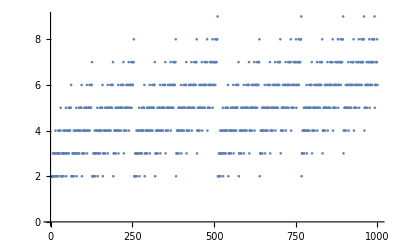

```mathematica
ListPlot[vals]
```

For fixed n, the number of terms in SumOfIntegerPowers[n,m] tends to increase as m increases. First, declare a (large-ish) integer:

```mathematica
large=849761218
```

849761218

Compute the lengths:

```mathematica
lengths=Table[Length[SumOfIntegerPowers[large,i]],{i,2,150}];
```

Plot them:

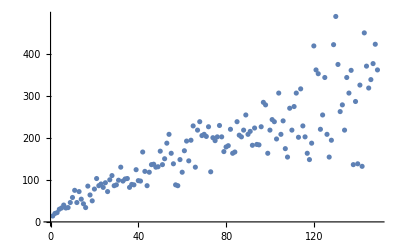

```mathematica
ListPlot[lengths]
```

The growth appears to be roughly linear. Test that observation:

```mathematica
lm=LinearModelFit[lengths,x,x]
```

FittedModel[35.3836+1.95327 x]

Check the goodness of fit, visually:

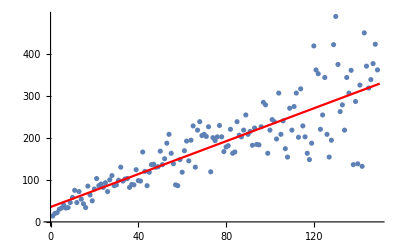

```mathematica
Show[{
ListPlot[lengths],
Plot[lm[x],{x,0,150},PlotStyle->Red]
}]
```

Check the goodness of fit mathematically as well:

```mathematica
lm["RSquared"]
```

0.712141

```mathematica
lm["AdjustedRSquared"]
```

0.710183

Create a multiplication table where SumOfIntegerPowers (and a little formatting) has been applied to each product. First, create the data:

```mathematica
nums=#&/@Table[Times[i, j],{i,0,12},{j,0,12}]/.{a_Integer:>Style[a,FontWeight->Bold]};
sums=SumOfIntegerPowers[#,{2,3}]&/@Table[Times[i, j],{i,0,12},{j,0,12}];
table=Table[Transpose[{%%[[i]],%[[i]]}],{i,1,13}]/.{List[Style[a_Integer,Rule[FontWeight,Bold]],b_]:>Column[List[Style[a,Rule[FontWeight,Bold]],b]]};
```

Then, display a stylized version of the table:

```mathematica
fulltable=TextGrid[
Join[{Join[{Item[Style["×", Larger], Background ->Lighter@ Orange,Alignment->Center]}, Table[i, {i, 0, 12}]]}, MapIndexed[Prepend[#1, First[#2] + 0 - 1] & , table]],
Frame -> All, FrameStyle -> Directive[GrayLevel[0.6]], Background -> {1 -> Lighter@LightOrange, 1 -> Lighter@LightOrange},ItemSize->{{{2,ConstantArray[13,13]/.{List->Sequence}}}},Alignment->{Left,Top},Spacings->{1,Automatic}]
```

× | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
0 | 0
2^(-∞)+3^(-∞) | 0
2^(-∞)+3^(-∞) | 0
2^(-∞)+3^(-∞) | 0
2^(-∞)+3^(-∞) | 0
2^(-∞)+3^(-∞) | 0
2^(-∞)+3^(-∞) | 0
2^(-∞)+3^(-∞) | 0
2^(-∞)+3^(-∞) | 0
2^(-∞)+3^(-∞) | 0
2^(-∞)+3^(-∞) | 0
2^(-∞)+3^(-∞) | 0
2^(-∞)+3^(-∞) | 0
2^(-∞)+3^(-∞)
1 | 0
2^(-∞)+3^(-∞) | 1
2^0 | 2
2^1 | 3
3^1 | 4
2^2 | 5
2^2+2^0 | 6
2^2+2^1 | 7
2^2+3^1 | 8
2^3 | 9
3^2 | 10
3^2+2^0 | 11
3^2+2^1 | 12
3^2+3^1
2 | 0
2^(-∞)+3^(-∞) | 2
2^1 | 4
2^2 | 6
2^2+2^1 | 8
2^3 | 10
3^2+2^0 | 12
3^2+3^1 | 14
3^2+2^2+2^0 | 16
2^4 | 18
2^4+2^1 | 20
2^4+2^2 | 22
2^4+2^2+2^1 | 24
2^4+2^3
3 | 0
2^(-∞)+3^(-∞) | 3
3^1 | 6
2^2+2^1 | 9
3^2 | 12
3^2+3^1 | 15
3^2+2^2+2^1 | 18
2^4+2^1 | 21
2^4+2^2+2^0 | 24
2^4+2^3 | 27
3^3 | 30
3^3+3^1 | 33
2^5+2^0 | 36
2^5+2^2
4 | 0
2^(-∞)+3^(-∞) | 4
2^2 | 8
2^3 | 12
3^2+3^1 | 16
2^4 | 20
2^4+2^2 | 24
2^4+2^3 | 28
3^3+2^0 | 32
2^5 | 36
2^5+2^2 | 40
2^5+2^3 | 44
2^5+3^2+3^1 | 48
2^5+2^4
5 | 0
2^(-∞)+3^(-∞) | 5
2^2+2^0 | 10
3^2+2^0 | 15
3^2+2^2+2^1 | 20
2^4+2^2 | 25
2^4+3^2 | 30
3^3+3^1 | 35
2^5+3^1 | 40
2^5+2^3 | 45
2^5+3^2+2^2 | 50
2^5+2^4+2^1 | 55
2^5+2^4+2^2+3^1 | 60
2^5+3^3+2^0
6 | 0
2^(-∞)+3^(-∞) | 6
2^2+2^1 | 12
3^2+3^1 | 18
2^4+2^1 | 24
2^4+2^3 | 30
3^3+3^1 | 36
2^5+2^2 | 42
2^5+3^2+2^0 | 48
2^5+2^4 | 54
2^5+2^4+2^2+2^1 | 60
2^5+3^3+2^0 | 66
2^6+2^1 | 72
2^6+2^3
7 | 0
2^(-∞)+3^(-∞) | 7
2^2+3^1 | 14
3^2+2^2+2^0 | 21
2^4+2^2+2^0 | 28
3^3+2^0 | 35
2^5+3^1 | 42
2^5+3^2+2^0 | 49
2^5+2^4+2^0 | 56
2^5+2^4+2^3 | 63
2^5+3^3+2^2 | 70
2^6+2^2+2^1 | 77
2^6+3^2+2^2 | 84
3^4+3^1
8 | 0
2^(-∞)+3^(-∞) | 8
2^3 | 16
2^4 | 24
2^4+2^3 | 32
2^5 | 40
2^5+2^3 | 48
2^5+2^4 | 56
2^5+2^4+2^3 | 64
2^6 | 72
2^6+2^3 | 80
2^6+2^4 | 88
3^4+2^2+3^1 | 96
3^4+3^2+2^2+2^1
9 | 0
2^(-∞)+3^(-∞) | 9
3^2 | 18
2^4+2^1 | 27
3^3 | 36
2^5+2^2 | 45
2^5+3^2+2^2 | 54
2^5+2^4+2^2+2^1 | 63
2^5+3^3+2^2 | 72
2^6+2^3 | 81
3^4 | 90
3^4+3^2 | 99
3^4+2^4+2^1 | 108
3^4+3^3
10 | 0
2^(-∞)+3^(-∞) | 10
3^2+2^0 | 20
2^4+2^2 | 30
3^3+3^1 | 40
2^5+2^3 | 50
2^5+2^4+2^1 | 60
2^5+3^3+2^0 | 70
2^6+2^2+2^1 | 80
2^6+2^4 | 90
3^4+3^2 | 100
3^4+2^4+3^1 | 110
3^4+3^3+2^1 | 120
3^4+2^5+2^2+3^1
11 | 0
2^(-∞)+3^(-∞) | 11
3^2+2^1 | 22
2^4+2^2+2^1 | 33
2^5+2^0 | 44
2^5+3^2+3^1 | 55
2^5+2^4+2^2+3^1 | 66
2^6+2^1 | 77
2^6+3^2+2^2 | 88
3^4+2^2+3^1 | 99
3^4+2^4+2^1 | 110
3^4+3^3+2^1 | 121
3^4+2^5+2^3 | 132
2^7+2^2
12 | 0
2^(-∞)+3^(-∞) | 12
3^2+3^1 | 24
2^4+2^3 | 36
2^5+2^2 | 48
2^5+2^4 | 60
2^5+3^3+2^0 | 72
2^6+2^3 | 84
3^4+3^1 | 96
3^4+3^2+2^2+2^1 | 108
3^4+3^3 | 120
3^4+2^5+2^2+3^1 | 132
2^7+2^2 | 144
2^7+2^4

Check the activated version for correctness:

```mathematica
Activate[fulltable/.{(ItemSize->_)->(ItemSize->{{Join[{2},ConstantArray[3,13]]}})}]
```

× | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0
1 | 0
0 | 1
1 | 2
2 | 3
3 | 4
4 | 5
5 | 6
6 | 7
7 | 8
8 | 9
9 | 10
10 | 11
11 | 12
12
2 | 0
0 | 2
2 | 4
4 | 6
6 | 8
8 | 10
10 | 12
12 | 14
14 | 16
16 | 18
18 | 20
20 | 22
22 | 24
24
3 | 0
0 | 3
3 | 6
6 | 9
9 | 12
12 | 15
15 | 18
18 | 21
21 | 24
24 | 27
27 | 30
30 | 33
33 | 36
36
4 | 0
0 | 4
4 | 8
8 | 12
12 | 16
16 | 20
20 | 24
24 | 28
28 | 32
32 | 36
36 | 40
40 | 44
44 | 48
48
5 | 0
0 | 5
5 | 10
10 | 15
15 | 20
20 | 25
25 | 30
30 | 35
35 | 40
40 | 45
45 | 50
50 | 55
55 | 60
60
6 | 0
0 | 6
6 | 12
12 | 18
18 | 24
24 | 30
30 | 36
36 | 42
42 | 48
48 | 54
54 | 60
60 | 66
66 | 72
72
7 | 0
0 | 7
7 | 14
14 | 21
21 | 28
28 | 35
35 | 42
42 | 49
49 | 56
56 | 63
63 | 70
70 | 77
77 | 84
84
8 | 0
0 | 8
8 | 16
16 | 24
24 | 32
32 | 40
40 | 48
48 | 56
56 | 64
64 | 72
72 | 80
80 | 88
88 | 96
96
9 | 0
0 | 9
9 | 18
18 | 27
27 | 36
36 | 45
45 | 54
54 | 63
63 | 72
72 | 81
81 | 90
90 | 99
99 | 108
108
10 | 0
0 | 10
10 | 20
20 | 30
30 | 40
40 | 50
50 | 60
60 | 70
70 | 80
80 | 90
90 | 100
100 | 110
110 | 120
120
11 | 0
0 | 11
11 | 22
22 | 33
33 | 44
44 | 55
55 | 66
66 | 77
77 | 88
88 | 99
99 | 110
110 | 121
121 | 132
132
12 | 0
0 | 12
12 | 24
24 | 36
36 | 48
48 | 60
60 | 72
72 | 84
84 | 96
96 | 108
108 | 120
120 | 132
132 | 144
144

## Source & Additional Information

### Contributed By

Christopher Stover

### Keywords

factor

factorize

sum of powers

exponents

prime powers

sum over lists

sequences

sums

series

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

FactorInteger

BaseForm

PrimePowerQ

Prime

### Related Resource Objects

InactiveFactorInteger

FormatFactorization

PerfectPower

Goldbach

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

MyFunction[x,y]

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

### v1.0.0

In future versions, better handling of the "power of list" case will be included. For instance, I would argue that

```mathematica
SumOfIntegerPowers[2^9*3^15*5, {2, 3, 5, 7}, "HoldListProducts" -> True]
```

2^9×3^15×5

should actually be something like

```mathematica
Inactive[Times][Inactive[Power][2,9],Inactive[Power][3,15],Inactive[Power][5,1],Inactive[Power][7,0]]
```

2^9×3^15×5^1×7^0

instead.

I already have a fix written for this. Whenever I implement it, I’ll be sure to edit info in "Options", D&O and any other places.

Design changes may be implemented to change the behavior discussed in "Possible Issues":

```mathematica
SumOfIntegerPowers[2^9*3^15*5,{2,3},"HoldListProducts"->True]
```

2^35+2^31+2^27+2^26+2^24+3^14+2^21+3^12+2^18+3^11+3^9+2^12+2^10+2^8+2^7+2^5+2^4+2^3

```mathematica
SumOfIntegerPowers[2^9*3^15*5,{2,3},"HoldListProducts"->False]
```

2^35+2^31+2^27+2^26+2^24+3^14+2^21+3^12+2^18+3^11+3^9+2^12+2^10+2^8+2^7+2^5+2^4+2^3

```mathematica
SumOfIntegerPowers[2^9*3^15*5,{2,3,5,7},"HoldListProducts"->True]
```

2^9×3^15×5

```mathematica
SumOfIntegerPowers[2^9*3^15*5,{2,3,5,7},"HoldListProducts"->False]
```

2^35+2^31+2^27+2^26+2^24+7^8+2^21+2^13+2^12+2^10+3^6+3^4+2^4+5^1

Perhaps these scenarios should be handled the same? Or perhaps the first situation should be handled differently if "HoldListProducts" and "Collect" are both set to True?

For non-infinite n, I may extend SumOfIntegerPowers[n,list] to allow list to contain 1. I don't have strong opinions about this currently but it may happen in the future.

## Submission Notes

Additional information for the reviewer.